# GABE NOTEBOOK : Spectra

Chris Shepherd, July 2020, christopher.shepherd-3@postgrad.manchester.ac.uk

Clear all variables to avoid naming conflicts.

```mathematica
ClearAll["Global`*"]
```

```mathematica
globalThickness=0.005;
globalFontSize=20;
globalFont="Latin Modern Mono Prop 10";
SetOptions[{ListPlot, ListLogPlot, Plot, LogPlot,ListLogLinearPlot,ListLogLogPlot,RegionPlot},LabelStyle->{ FontFamily->globalFont,FontSize-> globalFontSize, FontColor-> Black }, PlotStyle-> {Black, Thickness-> globalThickness}];

dirlabel={"17445_64_1000_125", "17445_32_1500", "17445_64_750"}; (*file name endings*)
numdirs=Length[dirlabel];
plotlabel="17445";
```

```mathematica
dir=Table[{"C:\\Users\\admin\\Documents\\PhD_work\\R2HI\\long_paper\\GABE\\friedmann\\local_results_"<>dirlabel[[k]]<>"\\slices\\", "C:\\Users\\admin\\Documents\\PhD_work\\GABE\\local_results_"<>dirlabel<>"\\slices\\"},{k,1,numdirs}];
ext=".dat";nflds=5;skip=1;

tspec={0,8,31,111,357,1138};
nPlots=Length[tspec];
dt=1;
specNum=tspec/dt;
Round[specNum]*dt ;(*check scalaron <0*)
specNumStr=Table[ToString[Round[specNum[[i]]]], {i,1,nPlots}];
```

## Plots of n_k

```mathematica
Clear[intablespec]
Clear[nspec]

nspec = ConstantArray[0, nPlots];
numbins = ConstantArray[0, {numdirs,nPlots}];
mm= ConstantArray[0, {numdirs,nPlots,5}];
intablespec= ConstantArray[0,{numdirs,nPlots}];
```

```mathematica
For[kk=1, kk<numdirs+1, kk++,
	For[ii=1, ii<nPlots+1, ii++,
	strT=specNumStr[[ii]];
	intablespec[[kk]][[ii]]=ReadList[dir[[kk]][[1]]<>"slices_spectra_"<>strT<>".dat", Table[ Real,{41}]];
	numbins [[kk]][[ii]]=Length[intablespec[[kk]][[ii]]]-1;
(*TODO: read in eigenvectors vectors off bottom line*)

		mm[[kk,ii,1]]= intablespec[[kk]][[ii]]⟦1,4⟧;
		mm[[kk,ii,2]]= intablespec[[kk]][[ii]]⟦1,12⟧;
	               mm[[1]][[ii]][[3]] = intablespec[[kk]][[ii]]⟦1,20⟧;
	mm[[1]][[ii]][[4]] = intablespec[[kk]][[ii]]⟦1,28⟧;
	 mm[[1]][[ii]][[5]] = intablespec[[kk]][[ii]]⟦1,36⟧;
]
]
```

```mathematica
nspec=Table[ConstantArray[0, {nPlots,nflds, numbins[[k,1]],2}], {k,1,numdirs}];
For[k=1, k<numdirs+1,k++,
For[ii=1, ii<nPlots+1,ii++,
For[fld=1, fld<nflds+1,fld++,
	For[i=1, i<numbins[[k,1]]+1, i++,
		nspec[[k]][[ii]][[fld]][[i]][[1]]=intablespec[[k]][[ii]][[i,1]];
		nspec[[k]][[ii]][[fld]][[i]][[2]]=Round[intablespec[[k]][[ii]][[i,6+8*(fld-1)]],0.01];
	];
	]
]
]//Quiet

k2nspec=Table[ConstantArray[0, {nPlots,nflds, numbins[[k,1]],2}], {k,1,numdirs}];
For[k=1,k<numdirs+1,k++,
For[ii=1, ii<nPlots+1,ii++,
For[fld=1, fld<nflds+1,fld++,
	For[i=2, i<numbins[[k,1]]+1, i++,
		k2nspec[[k,ii]][[fld]][[i]][[1]]=intablespec[[k,ii]][[i,1]] ;
		k2nspec[[k,ii]][[fld]][[i]][[2]]=(intablespec[[k,ii]][[i,1]])^2*Round[intablespec[[k]][[ii]][[i,6+8*(fld-1)]],0.01];
	];
	]
]
]//Quiet
k3nspec=Table[ConstantArray[0, {nPlots,nflds, numbins[[k,1]],2}], {k,1,numdirs}];
For[k=1,k<numdirs+1,k++,
For[ii=1, ii<nPlots+1,ii++,
For[fld=1, fld<nflds+1,fld++,
	For[i=2, i<numbins[[k,1]]+1, i++,
		k3nspec[[k,ii]][[fld]][[i]][[1]]=intablespec[[k,ii]][[i,1]] ;
		k3nspec[[k,ii]][[fld]][[i]][[2]]=(intablespec[[k,ii]][[i,1]])^3*Round[intablespec[[k]][[ii]][[i,6+8*(fld-1)]],0.00001];
	];
	]
]
] (*integrand in total inhomogeneous energy, proportional to \int dk {k^3 n_k}*)

k2rhospec=Table[ConstantArray[0, {nPlots,nflds, numbins[[k,1]],2}], {k,1,numdirs}];
For[k=1,k<numdirs+1,k++,
For[ii=1, ii<nPlots+1,ii++,
For[fld=1, fld<nflds+1,fld++,
	For[i=2, i<numbins[[k,1]]+1, i++,
		k2rhospec[[k,ii]][[fld]][[i]][[1]]=intablespec[[k,ii]][[i,1]] ;
		k2rhospec[[k,ii]][[fld]][[i]][[2]]=(intablespec[[k,ii]][[i,1]])^2*Sqrt[intablespec[[k]][[ii]][[i,5+8*(fld-1)]]]*Round[intablespec[[k]][[ii]][[i,6+8*(fld-1)]],0.0001];
	];
	]
]
] (*basically the same object as above, but masses change with time, so hard to compare different times to one another*)
```

Plotting from first directory

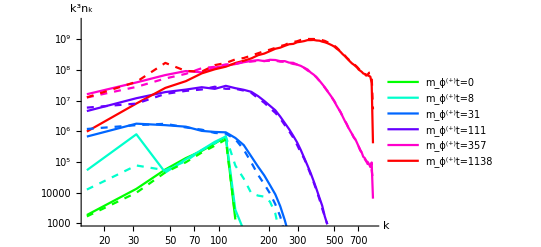

```mathematica
q3nPlot=Show[{Show[Table[ListLogLogPlot[k3nspec[[1,ii]][[2]], Joined->True, PlotStyle->{Hue[.2+((.8ii)/nPlots)]}, PlotLegends->LineLegend[{Hue[.2+(.8ii)/nPlots]},{"m_ϕ^(+)t="<>ToString[tspec[[ii]]]}]], {ii,1,nPlots}],AxesLabel-> {"k", "k^3n_k"},PlotRange-> All],
Show[Table[ListLogLogPlot[k3nspec[[1,ii]][[3]], Joined->True, PlotStyle->{Dashed,Hue[.2+.8ii/nPlots]}], {ii,1,nPlots}],AxesLabel-> {"q", "q^3n_q"},PlotRange-> All], AxesOrigin-> {Exp[.9],8}, PlotRange-> {7, 22}}
]
(*SetDirectory["C:\\Users\\admin\\documents\\PhD_work_R2HI\\long_paper\\paper\\new_figures"];
Export["spectra_"<>plotlabel<>".pdf", q3nPlot];*)
```

Plotting from different directories

```mathematica
nAll=Table[Table[ListLogLogPlot[nspec[[kk,ii,2]], Joined->True, PlotStyle->Hue[kk/numdirs]], {kk,1,numdirs}], {ii,1,nPlots}];
q3nAll=Table[Table[ListLogLogPlot[k3nspec[[kk,ii,2]], Joined->True, PlotStyle->Hue[kk/numdirs]], {kk,1,numdirs}], {ii,1,nPlots}];
```

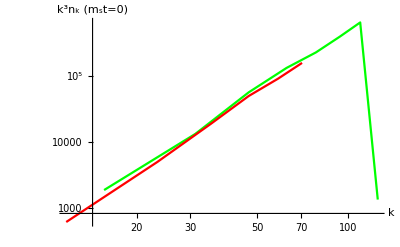

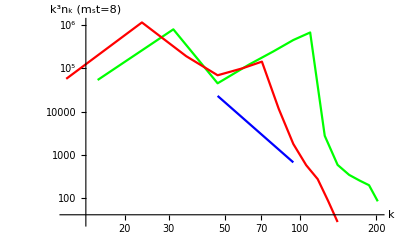

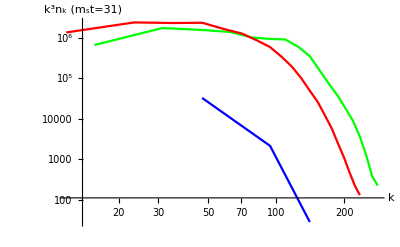

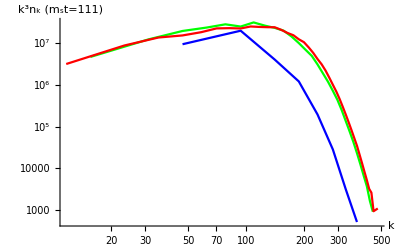

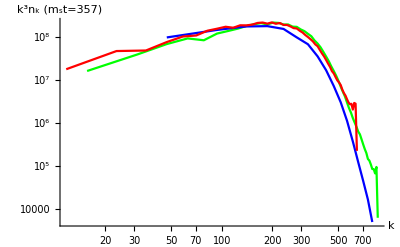

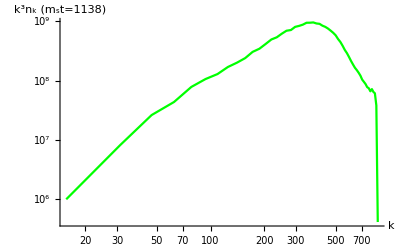

```mathematica
(*For[ii=1, ii<nPlots+1, ii++,
(*Print[Show[nAll[[ii]], PlotRange-> {All, Automatic}, AxesLabel-> {"q", "n_q (m_st="<>ToString[tspec[[ii]]]<>")" }] ];*)
(*Print[Show[q3nAll[[ii]], PlotRange-> {All, Automatic}, AxesLabel-> {"q", "q^3n_q (m_st="<>ToString[tspec[[ii]]]<>")" }] ];*)
Print[ Show[nAll[[ii]], PlotRange-> All, AxesLabel-> {"q", "n_q (m_st="<>ToString[tspec[[ii]]]<>")"}] ]
]*)
For[ii=1, ii<nPlots+1, ii++,
(*Print[Show[nAll[[ii]], PlotRange-> {All, Automatic}, AxesLabel-> {"q", "n_q (m_st="<>ToString[tspec[[ii]]]<>")" }] ];*)
Print[Show[q3nAll[[ii]], PlotRange-> {All, Automatic}, AxesLabel-> {"k", "k^3n_k (m_st="<>ToString[tspec[[ii]]]<>")" }]]
]
```